# Mathematica Lab 3-Properties Laplace Transform Representation

## Property-Time Scaling (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *07.12.2022*

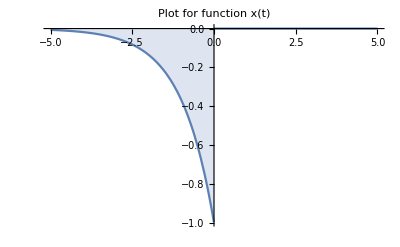

ConditionalExpression[-1/(1-s), Re[s]<1]

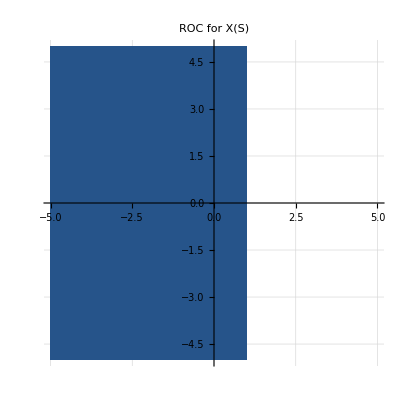

```mathematica
x[t_]:=-Exp[t]UnitStep[-t];
(* This is Signal 1. *)
(* We are defining the signal itself here. *)
(* This signal is defiened in the TIME domain! *)

P1=Plot[x[t],{t,-5,5},Filling->Axis,PlotRange->All,PlotLabel->"Plot for function x(t)"]
(* We Plot the signal function. See graph plot. *)

X[s_]=∫_(-∞)^∞ x[t]Exp[-s t]ⅆt
(* This defines the Laplace transform: *)

ROC=FullSimplify[(X[s]/Normal[X[s]])/.s->σ+ⅉ ω];
PX=ContourPlot[ROC,{σ,-5,5},{ω,-5,5},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for X(S)"]
(* This plots the Region of Convergence-ROC: *)
```

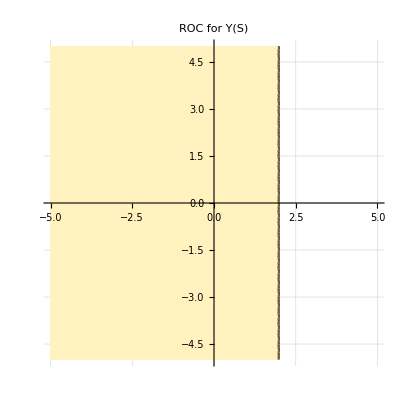

```mathematica
a=2; (* We take a value for a to more easily calculate the graph outputs, becasue otherwise the code takes a very long time to run. *)
Y[s_]:= 1/Abs[a]* X[s/a];
(* Here we use Table TABLE-9.1 PROPERTIES OF THE LAPLACE TRANSFORM to get the Laplace Transform Property of Time Scaling. *)
(* 9.5.4 *) (* We define this into a function Y(s) which is a function of X(s). *)

ROC=FullSimplify[(Y[s]/Normal[Y[s]])/.s->σ+ⅉ ω];
PY=ContourPlot[ROC,{σ,-5,5},{ω,-5,5},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for Y(S)"]
(* This plots the Region of Convergence-ROC: *)
```

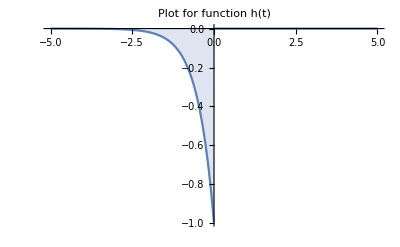

ConditionalExpression[-1/(2-s), Re[s]<2]

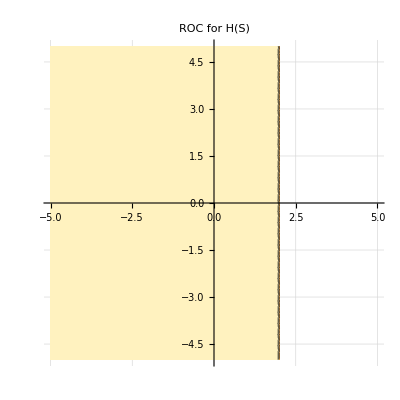

```mathematica
h[t_]=x[a*t];
(*  Here we are expressing the property of the signal in the TIME domain-normally using the given formula.  *)
(* We can see the scalar "a" compresses or widens the function. In this case it is 2, so it compresses it by a factor of 2, as seen in the graph below! *)

P2=Plot[h[t],{t,-5,5},Filling->Axis,PlotRange->All,PlotLabel->"Plot for function h(t)"]
(* We Plot the signal function. See graph plot. *)

H[s_]=∫_(-∞)^∞ h[t]Exp[-s t]ⅆt
(* This defines the Laplace transform: *)

ROC=FullSimplify[(H[s]/Normal[H[s]])/.s->σ+ⅉ ω];
PH=ContourPlot[ROC,{σ,-5,5},{ω,-5,5},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic, PlotLabel->"ROC for H(S)"]
(* This plots the Region of Convergence-ROC: *)
```

```mathematica
Simplify[Y[s]==H[s]]   (* We prove this is TRUE with both approaches, thus we prove the proeprty, for the ROC. *)
```

ConditionalExpression[True, Re[s]<2]

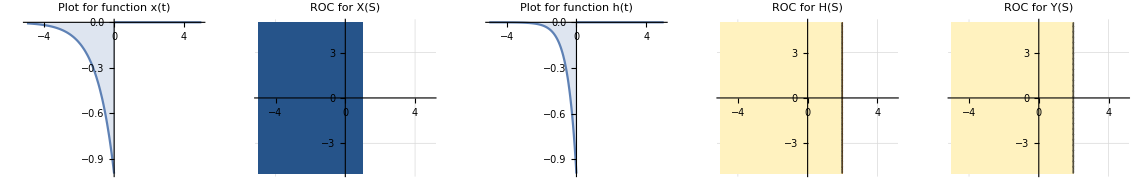

```mathematica
GraphicsGrid[{{P1,PX,P2,PH, PY}},Frame->True] (* Zoom out or scroll left to see all graphs. And we can compare ROC and functions Y[s] and H[s] visually and see they are the same, thus the property is TRUE. *)
```